```mathematica
?BinomialDistribution
```

BinomialDistribution[n,p] represents a binomial distribution with n trials and success probability p.

```mathematica
CDF[BinomialDistribution[18,p]][10]*CDF[BinomialDistribution[29,1-p]][7]
```

BetaRegularized[1-p,8,11] BetaRegularized[p,22,8]

```mathematica
CDF[BinomialDistribution[18,0.6868824802728842]][10]*CDF[BinomialDistribution[29,1-0.6868824802728842]][7]
```

0.0459072

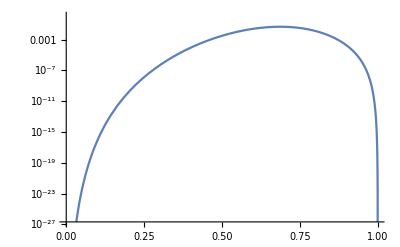

```mathematica
LogPlot[BetaRegularized[1-p,8,11] BetaRegularized[p,22,8],{p,0,1}]
```

```mathematica
D[BetaRegularized[1-p,8,11] BetaRegularized[p,22,8],p]
```

34337160 (1-p)^7 p^21 BetaRegularized[1-p,8,11]-350064 (1-p)^7 p^10 BetaRegularized[p,22,8]

```mathematica
FindRoot[34337160 (1-p)^7 p^21 BetaRegularized[1-p,8,11]-350064 (1-p)^7 p^10 BetaRegularized[p,22,8],{p,.7}]
```

{p→0.686882}

```mathematica
(* 36% correct: 17 of 47
winter guessed 32: winter 10 spring 22
spring guessed 15: winter  8 spring  7 
total 47:          winter 18 spring 29*)

(* winter 18: guessed winter 10 spring  8
 spring 29: guessed winter 22 spring  7*)
```

```mathematica
CDF[BinomialDistribution[18,32/47]][10]*CDF[BinomialDistribution[29,15/47]][7]
```

177466098331784471623635487171194215289066102566560647351849596642918400000000/3877924263464448622666648186154330754898344901344205917642325627886496385062863

```mathematica
%//N
```

0.0457632

```mathematica
32/47.
```

0.680851